## Definitions

```mathematica
op[x_,loc_]:=Text[Style[x,13,Bold,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_]:=Text[Style[x,13,weight,Italic,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_,color_]:=Text[Style[x,13,weight,color,Italic,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
fsize=14
```

14

```mathematica
size:=120;
```

```mathematica
sb=.07( 120/size); ah=.04;
```

```mathematica
{size,ah,sb}//N
```

{120.,0.04,0.07}

```mathematica
Text[Style[α, 16], .5(la+lb),Background->White]
```

```mathematica
lab[n_,p1_,p2_]:=Text[Style[StringJoin[" ",ToString[n]," "],fsize,FontFamily->"Arial"],.5(p1+p2),Background->White]
```

## Construction of commutative squares

```mathematica
la={0,1};ra={1,1};
lb={0,0};rb={1,0};
rra={2,1};rrb={2,0};
```

```mathematica
funcdi[list_,size_]:=Framed[Graphics[
{Arrowheads[Medium],list},
ImageSize->size,FrameTicks->False],FrameMargins->Tiny, FrameStyle->White]
```

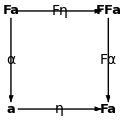

```mathematica
firstdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb]},{size,size}]
```

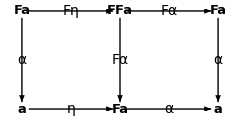

```mathematica
seconddi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Arrow[{rb,rrb},sb],lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb],lab[Fα,ra,rra],lab[α,rra,rrb],lab[α,rb,rrb]},{2 size,size}]
```

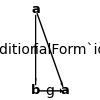

```mathematica
elevdi=funcdi[{op["a",la],op["b",lb],op["a",rb],
Arrow[{la,rb},sb],Arrow[{la,lb},sb],Arrow[{lb,rb},sb],lab[f,la,lb],lab[g,lb,rb],lab[Subscript[id, a]//TraditionalForm,la,rb]},{100,100}]
```

## Cographs of finite functions

```mathematica
funcdi[{op["1",{0,2}],op["2",{0,1}],op["3",{0,0}],op["1",{2,2}],op["2",{2,1}],op["3",{2,0}],op["4",{2,-1}]},70]
```

-Graphics-

### Bijective1

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["1",d1],op["2",d2],op["3",d3],op["4",d4],op["1",c1],op["2",c2],op["3",c3],op["4",c4],Arrow[{d1,c3},sb],Arrow[{d2,c1},sb],Arrow[{d3,c4},sb],Arrow[{d4,c2},sb]},80]]
```

-Graphics-

### Surjective1

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["1",d1],op["2",d2],op["3",d3],op["4",d4],op["1",c1],op["2",c2],op["3",c3],Arrow[{d1,c3},sb],Arrow[{d2,c1},sb],Arrow[{d3,c2},sb],Arrow[{d4,c2},sb]},80]]
```

-Graphics-

### Neither1

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["1",d1],op["2",d2],op["3",d3],op["4",d4],op["1",c1],op["2",c2],op["3",c3],Arrow[{d1,c3},sb],Arrow[{d2,c2},sb],Arrow[{d3,c2},sb],Arrow[{d4,c2},sb]},80]]
```

-Graphics-

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["1",d1],op["2",d2],op["3",d3],op["1",c1],op["2",c2],op["3",c3],op["4",c4],Arrow[{d1,c3},sb],Arrow[{d2,c1},sb],Arrow[{d3,c4},sb]},80]]
```

-Graphics-

### Injective2

-Graphics-

### Increasing function for http://abstractmath.org/MM/MMMathStructure.htm

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["3",d2],op["2",d3],op["1",d4],op["4",c1],op["3",c2],op["2",c3],op["1",c4],Arrow[{d4,c4},sb],Arrow[{d3,c3},sb],Arrow[{d2,c1},sb]},80]]
```

-Graphics-

### Not a function

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["1",d1],op["2",d2],op["3",d3],op["4",d4],op["1",c1],op["2",c2],op["3",c3],op["4",c4],Arrow[{d1,c3},sb],Arrow[{d2,c1},sb],Arrow[{d4,c3},sb]},80]]
```

-Graphics-

```mathematica
Module[{sb=.2,d1={0,3},d2={0,2},d3={0,1},d4={0,0},c1={1.5,3},c2={1.5,2},c3={1.5,1},c4={1.5,0}},funcdi[{op["a",d1],op["b",d2],op["c",d3],op["d",d4],op["a",c1],op["b",c2],op["c",c3],op["d",c4],Arrow[{d1,c1},sb],Arrow[{d2,c3},sb],Arrow[{d3,c3},sb],Arrow[{d4,c2},sb]},80]]
```

-Graphics-

## partitions

```mathematica
Show[Graphics[{EdgeForm[Thick],
White,Rectangle[],
Rectangle[{1.5,0},{2.5,1}],Rectangle[{3,0},{4,1}],
Black,Text["1",{.25,.66}],Text["1",{.25,.66}],Text["4",{.75,.66}],Text["7",{.5,.33}],Text["2",{1.75,.5}],Text["5",{2.25,.5}],Text["3",{3.25,.5}],Text["6",{3.75,.5}]
}],
ImageSize->200]
```

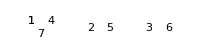

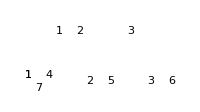

```mathematica
Show[Graphics[{EdgeForm[Thick],
White,Rectangle[],
Rectangle[{1.5,0},{2.5,1}],Rectangle[{3,0},{4,1}],
Black,Text["1",{.25,.66}],Text["1",{.25,.66}],Text["4",{.75,.66}],Text["7",{.5,.33}],Text["2",{1.75,.5}],Text["5",{2.25,.5}],Text["3",{3.25,.5}],Text["6",{3.75,.5}],White, Rectangle[{.75,1.25},{1.75,2.25}],
Rectangle[{2.25,1.25},{3.25,2.25}],
Black,Text["1",{1,1.75}],
Text["2",{1.5,1.75}],Text["3",{2.75,1.75}]
}],
ImageSize->200]
```

```mathematica
Show[Graphics[{EdgeForm[Thick],
White,Rectangle[],
Rectangle[{1.5,0},{2.5,1}],Rectangle[{3,0},{4,1}],
Black,Text["1",{.25,.66}],Text["1",{.25,.66}],Text["4",{.75,.66}],Text["7",{.5,.33}],Text["2",{1.75,.5}],Text["5",{2.25,.5}],Text["3",{3.25,.5}],Text["6",{3.75,.5}],White, Rectangle[{.75,1.25},{1.75,2.25}],
Rectangle[{2.25,1.25},{3.25,2.25}],
Black,Text["1",{1,1.75}],
Text["2",{1.5,1.75}],Text["3",{2.75,1.75}]
}],
ImageSize->200]
```